LUCAS LARSSON, DENNIS HADZIALIC
INLÄMNINGSUPPGIFT 1 

Polyniomekvationen:

```mathematica
polynom= 
Solve[x^5+23/3 x^4+25/3 x^3-107/3 x^2-148/3 x+20==0,x]
```

{{x→-5},{x→-3},{x→-2},{x→1/3},{x→2}}

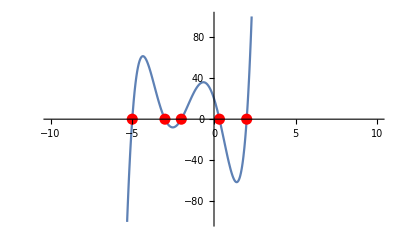

```mathematica
p1 = Plot[
x^5+(23/3)*x^4+(25/3)*x^3-(107/3)*x^2-(148/3)*x+20==0,
{x,-10,10}, PlotRange->{-100,100}, Epilog->{
Red, PointSize[0.02],
Point[{{-5,0},{-3,0},{-2,0},{1/3,0},{2,0}}]
}
]
```

### Olikhet:

### Uppgift 9

```mathematica
A)
```

```mathematica
Reduce[2+x>6 x^2]
```

-1/2<x<2/3

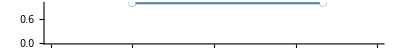

```mathematica
NumberLinePlot[-1/2<x<2/3,{x,-1,1}]
```

B)

```mathematica
Reduce[(1+x)/((-2+x) (3+2 x))≥0]
```

-3/2<x≤-1||x>2

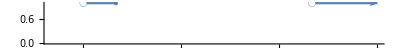

```mathematica
NumberLinePlot[-3/2<x≤-1||x>2,{x,-2,3}]
```

C)

```mathematica
Reduce[(x^2-5)/(x-1)≤-1]
```

x≤-3||1<x≤2

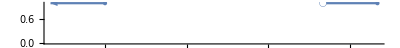

```mathematica
NumberLinePlot[x≤-3||1<x≤2,{x,-4,2}]
```

D)

```mathematica
Reduce[-√(x^2+9)≥2 √x+4]
```

False

```mathematica
NumberLinePlot[-√(x^2+9)≥2 √x+4,{x,-100,100}]
```

-Graphics-

“Tallinjen visar inget eftersom predikatet är Falskt.”

E)

```mathematica
Reduce[√(3x+3)≥√x+1]
```

x≥0

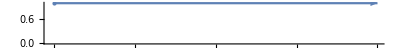

```mathematica
NumberLinePlot[x≥0,{x,-1,100}]
```

```mathematica
Uppgift 10
```

A)

```mathematica
Reduce[x^3<1&&-6-x+x^2≥0]
```

x≤-2

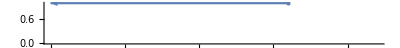

```mathematica
NumberLinePlot[x^3<1&&-6-x+x^2≥0,{x,-10,1}]
```

B)

```mathematica
Reduce[(2x-1)(x-3)(2x-5)==0&&√(x^2-x-2)≥2]
```

x==3

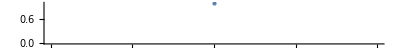

```mathematica
NumberLinePlot[(2x-1)(x-3)(2x-5)==0&&√(x^2-x-2)≥2,{x,2,4}]
```

C)

```mathematica
Reduce[√(x^2-x-2)≥√x&&x^2-1≥0]
```

x≥1+√3

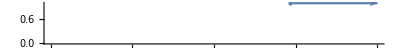

```mathematica
NumberLinePlot[x≥1+√3,{x,2,3}]
```

Binomisk Ekvation:

```mathematica
Clear[z]
z = z /.Solve[z^6==-3+3ⅈ]//N
```

{-1.1755-0.486907 ⅈ,1.1755+0.486907 ⅈ,-0.166075-1.26146 ⅈ,0.166075+1.26146 ⅈ,1.00942-0.774557 ⅈ,-1.00942+0.774557 ⅈ}

```mathematica
t = Table[{Re[Z⟦i⟧],Im[Z⟦i⟧]},{i,1,6}]
```

{{-1.1755,-0.486907},{1.1755,0.486907},{-0.166075,-1.26146},{0.166075,1.26146},{1.00942,-0.774557},{-1.00942,0.774557}}

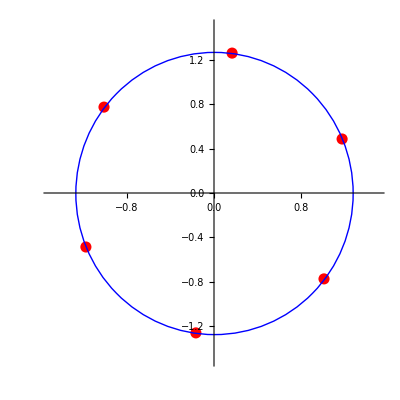

```mathematica
ListPlot[
t,
PlotRange->{
{-1.5, 1.5}, {-1.5, 1.5}
},
AspectRatio->1,
PlotStyle->{
PointSize[0.02],
RGBColor[1,0,0]
},
Epilog->{
RGBColor[0,0, 1],
Circle[
{0,0},
Abs[z[[1]]]
]
}
]
```

Logic:
1) 
        B) Vilka av dessa propositioner är sanna?

```mathematica
p1: (√2∈ℝ)∧∼(√2∈Q)
```

```mathematica
FullSimplify[Element[√2,Reals]&& !Element[√2,Rationals]]
```

True

```mathematica
p2: (1/2 ∈Z) ∨ (1/2∈Q) 
FullSimplify[Element[1/2,Integers]∨ Element[1/2,Rationals]]
```

True

```mathematica
p3:~(-4∈N)⟶~(-4∈Z) 
Implies[!NonNegative[-4],!Element[-4,Integers]]
```

False

```mathematica
p4: 2.5∈Q↔ 2.5∈R
```

Element::argrx: Element called with 3 arguments; 2 arguments are expected.

```mathematica
Equivalent[Element[5/2,Rationals],Element[2.5,Reals]]
```

True

Ekvationlösning och grafer: 

En D’Artagnan jagas av Richeliue. Båda rider så snabbt de kan. D’Artagnan rider med en hastighet av 42 km/h och Richeliue med 57 km/h. Richeliue är 60 meter efter D’Artagnan och det är 250 meter till stadsporten där D’Artagnan kan komma undan. Bestäm om Richeliue hinner i kapp D’Artagnan och i så fall vilken tidpunkt och sträcka innan stadsporten det sker. Illustrera tidsförloppet grafiskt på lämpligt sätt.

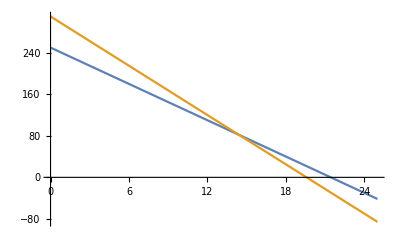

```mathematica
functionDa[x_]:=250-(42/3.6)x
functionRi[x_]:=310-(57/3.6)x
Plot[{functionDa[x],functionRi[x]}, {x,0,25}]
```

```mathematica
Solve[functionDa[x]==functionRi[x]]
```

{{x→14.4}}

```mathematica
functionDa[14.4]
```

82.

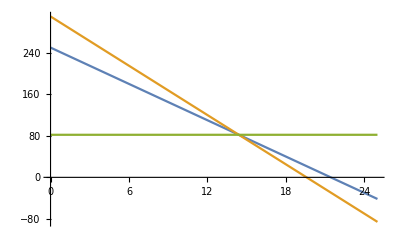

```mathematica
Plot[{functionDa[x],functionRi[x],82},{x,0,25}]
```

Svar : 82 meters / 14.4 sekunders marginal hinner Richeliue med D’Artagnan.

# Rapport:

## Polynomekvation

Ekvationen löstes med hjälp av Solve funktionen. Ekvationen ger 5 olika lösningar eftersom det är en polynomekvation av 5:e grad. Sedan “plottas” lösningar som visar nollställen och därefter markeras de med rödapunktar med användig av lämpliga kommandon i funktionen PlotStyle.

## Olikhet

Samtliga uppgifter (Uppgift 9: A,B,C,D,E och Uppgift 10: A,B,C) löstes med hjälp av REDUCE-funktionen, därefter “plottas” de med funktionen (NumberLinePlot) för att  beskriva informationen (lösningar) på ett tydligare sätt.

## Binomiska Ekvation

Ekvationen  z^6=-3+3  ⅈ löstes med SOLVE-funktionen och sedan “ //N” används för att uttrycka det numeriska värdet av lösningen. 
Eftersom det är ett 6-gradig funktion så produceras 6 olika lösningar.

 De lösningar tilldelas en variabel “t” ,
 Table[{Re[Z⟦i⟧],Im[Z⟦i⟧]}]  Anger/ konverterar lösningar från komplexa-tal-form till en {x,y} kordinat lista som kan plottas vanligt, 
 
 PlotRange: Ändrar skalan på grafen, 
 PlotStyle: Modlerar utseende av garafen,
 ABS: Anger det absoluta beloppet.
 
 Finns en annan funktion man kan använda som heter ComplexListPlot istället men den hade vi problem med att få att fungera.

## Logik

UPPGIFT :  1  -B

Uppgiften är om 4 Predikater som ska prövas om de är sanna eller falska. 
• p1 och p2 prövas med hjälp av samma funktion “FullSimplify”  pridekaterna skrivs om i form som matimatika kan förstå. Båda pridikaten är sanna. 
• p3 pridikaten prövas om den är sanna med hjläp av “Implies” vilket visar att det är falskt predikat. 
• p4 predikaten prövas om den är sann med hjälp av “Equivalent-funktionen” som visar att den är sann.

## Ekvationlösning och Grafer

I denna uppgift  beskrivs ett problem där en D’Artagnan som  jagas av  en Richeliue hinner till en viss punkt innan Richeliue hinner med honom och i så fall vid vilket punket respektive tid.  

Richeliue rider med 57 km/h
 D’Artagnan rider med 42 km/h 
 Richeliue är 60 meter efter D’Artagnan och det är 250 meter till den punkten där  D’Artagnan kan komma undan. 
 
En matimatisk modell måste byggas. 
 
 ▸ functionDa[x_]:=250-(42/3.6)x denna funktionen beskriver D’Artagnan. 
 ▸ fRi[x_]:=310-(57/3.6)x denna funktion beskriver Richeliue.
 Båda funktionerna plottas och den punkten där de korsar varandra (där funktionerna är lika med varandra) är den punkten där Richeliue hinner med D’Artagnan om han nu skulle hinna. 
 
 Lösning av funktionen visar att den hinner och visar även den specifika punkten på avsånd, respektive tid. 
 Funktionerna plottas för att visa lösningar grafiskt enligt kraven i uppgifen.